## Piezo driver noise analysis

Useful references: 
* http://www.ti.com/lit/an/sboa066a/sboa066a.pdf
* http://www.ti.com/lit/an/slva043b/slva043b.pdf

### Preliminaries/Constants

```mathematica
(* import and configure MaTeX, for using latex in mathematica plots *)
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/texbin/pdflatex","Ghostscript"->"/usr/local/Cellar/ghostscript/9.16/bin/gs"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb} \\usepackage{siunitx} \\DeclareSIUnit{\\sqrthz}{\\ensuremath{\\sqrt{\\text{\\hertz}}}}","\\usepackage{color,txfonts}"}];

texStyle={FontFamily->"Latin Modern Roman",FontSize->16};

(* keep mathematica from complaining in interpolating functions *)
Off[InterpolatingFunction::dmval]

(* set directory path *)
SetDirectory[NotebookDirectory[]];

(* constants, etc. *)
c=299792458;
kB=1.38064852*^-23;
hbar=1.0545718*^-34;
ϵ0=8.85418782*^-12;
a0=.52917721092*^-10;
e=1.602176487*^-19;
pp=1.*^-12;
nn=1.*^-9;
uu=1.*^-6;
mm=1.*^-3;
kk=1.*^3;
MM=1.*^6;
GG=1.*^9;

(* parallel impedances *)
par[z1_,z2_]:=z1 z2/(z1+z2);
```

### LM7171

The LM7171 is a very high speed, high slew-rate op amp.

```mathematica
OLG:=10.^(85/20); (* open loop gain, = 85dB *)
SR:=4100/uu (*slew rate, V/us*)
Vos:=0.2 mm (* Input offset voltage *)
VosTc:=35uu(*input offset voltage drift, V/degC*)
Ib:=2.7uu (* input bias current *)
Ios:=0.1uu (* input offset current *)
CMRR:=10.^(105/20) (* = 105dB, common mode rejection ratio *)
PSRR:=10.^(90/20) (* = 90dB, power supply rejection ratio *)
en:=14nn (* @10kHz, input-referred voltage noise, V/√Hz *)
in:=1.5pp (* @10kHz, input-referred current noise, A/√Hz *)
VnDAC:=100nn (* @ 1 kHz, conservative @ 10kHz; dac noise *)
```

#### Noise import

```mathematica
VnoiseImg=Binarize[Import["LM7171VoltNoise.png"]]
```

-Graphics-

Pull points off graph. {vy, vx, vo} are the coordinates of the y, x, and origin (axes), for coordinate transformation.
Vcurve is a sequence of points from the curve itself.
To get these off the graph, double click and select “coordinates tool”.
From that list of pixel coordinates, do a transformation to get into units of nV/rtHz.

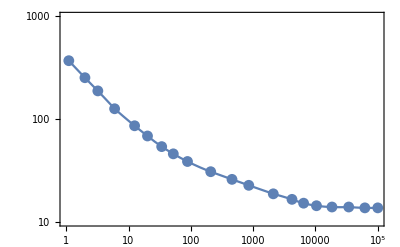

```mathematica
{vy,vx,vo}={{240,16},{723,499},{240,499}};
Vcurve={{723,466},{703,466},{678,464},{652,464},{628,461},{608,455},{590,446},{561,433},{523,413},{497,399},{464,381},{428,357},{406,339},{388,322},{366,297},{346,273},{315,233},{289,191},{269,160},{244,120}};

(* coordinate transformation; working in log units *)
Vtransform=FindGeometricTransform[{{0,1},{5,1},{0,3}},{vo,vx,vy}][[2]];
VptsLog=Vtransform@Vcurve;
Vpts=Map[10^#&,VptsLog,{2}];
(* VinterpolationLog is the voltage noise interpolating function *)
VinterpolationLog=Interpolation[VptsLog,InterpolationOrder->2];

(* plot along with extracted points to make sure the interpolation worked ok *)
Vplt=ListLogLogPlot[Vpts,PlotRange->{{1,100000},{10,1000}},Frame->True,GridLines->Automatic];
Show[Vplt,LogLogPlot[10^VinterpolationLog[Log10[x]],{x,1,10^5}]]
```

Now, we do the same thing with the current noise:

```mathematica
InoiseImg=Binarize[Import["LM7171CurrNoise.png"]]
```

-Graphics-

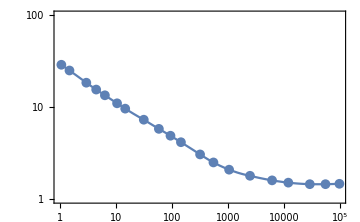

```mathematica
{iy,ix,io}={{184,9},{667,493},{184,493}};
Icurve={{666,452},{642,453},{615,453},{578,449},{550,443},{512,431},{476,415},{449,396},{426,375},{393,343},{375,326},{355,308},{329,284},{297,255},{283,241},{262,220},{247,205},{230,187},{201,155},{187,140}};
(* coordinate transformation; working in log units *)
Itransform=FindGeometricTransform[{{0,0},{5,0},{0,2}},{io,ix,iy}][[2]];
IptsLog=Itransform@Icurve;
Ipts=Map[10^#&,IptsLog,{2}];
IinterpolationLog=Interpolation[IptsLog,InterpolationOrder->2];
Iplt=ListLogLogPlot[Ipts,PlotRange->{{1,100000},{1,100}},Frame->True,GridLines->Automatic];
Show[Iplt,LogLogPlot[10^IinterpolationLog[Log10[x]],{x,1,10^5}]]
```

And one more time for the DAC noise:

```mathematica
DacNoiseImg=Binarize[Import["AD5663RVoltNoise.png"]]
```

-Graphics-

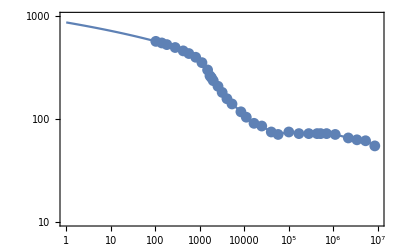

```mathematica
{dy,dx,do}={{155,48},{903,645},{155,645}};
DACcurve={{893,604},{862,599},{833,598},{804,596},{760,592},{731,591},{711,591},{699,591},{671,591},{638,591},{604,589},{568,592},{545,589},{513,581},{487,577},{461,567},{443,557},{413,540},{396,527},{380,509},{366,489},{350,468},{344,456},{339,448},{331,420},{312,380},{291,346},{268,320},{249,300},{222,273},{194,248},{177,233},{157,218}};
(*coordinate transformation;working in log units only in x*)DACtransform=FindGeometricTransform[{{2,0},{7,0},{2,800}},{do,dx,dy}][[2]];
DACptsLog=DACtransform@DACcurve;
DACpts=Map[{10^#[[1]],#[[2]]}&,DACptsLog];
DACinterpolationLog=Interpolation[DACptsLog,InterpolationOrder->1];
DACplt=ListLogLogPlot[DACpts,PlotRange->{{1,10^7},{10,1000}},Frame->True,GridLines->Automatic];
Show[DACplt,LogLogPlot[DACinterpolationLog[Log10[x]],{x,1,10^7}]]
```

### Noise analysis

We have the following op amp model:

```mathematica
Clear[s];
R1=1MM;
C1=1nn;
R2=20.5kk;
Rmod=1MM;
Cmod=1nn;

Rlp=20.5kk;
Zlp=par[par[(1/(s 10uu)+0.7),1/(s 47nn)],1MM];(* effective Z -- see full circuit for details -- Ron resistance is 0.7 ohms for part*)

Z1=par[R1,1/(C1 s)];
Z2 = R2;
Zmod = par[Rmod, 1/(Cmod s)];

(* impedance seen at non-inverting node *)
Zp=par[Rlp,Zlp];
(* impedance seen at inverting node *)
Zn=par[par[Z2,Zmod],Z1];

NG=1+Z1/(par[Z2,Zmod]); (* noise gain *)
Ginv=Z1/par[Z2,Zmod]; (* gain at inverting input node *)
Gmod=Z1/Zmod;(* modulation gain *)
Gdc=Zlp/(Rlp+Zlp)(1+Z1/(par[Z2, Zmod])) ;(* LP filter * non-inverting gain*)
```

Now, actually compute noise as a function of frequency:

```mathematica
T=300;(* assume temperatures computed at 300K *)
JohnsonNoise=NG(4 kB T (Re[Zn] +Re[Zp] ))^(1/2);(* Johnson noise *)


(* construct noise gain, impedances, etc. as functions *)
NoiseGain[s_]=NG//FullSimplify;
ZZp[s_]=Zp//FullSimplify;
ZZn[s_]=Zn//FullSimplify;
JJNoise[s_]=JohnsonNoise//FullSimplify;
GDCInp[s_]=Gdc//FullSimplify;

(* compute the current, voltage, DAC noise. The Johnson noise is contributed directly at the output. be careful about angular vs real frequency units!
Now, here, s is a real frequency (easier for plotting, also what interpolating functions use).
 *)
CurrNoiseOpAmp[s_]:=NoiseGain[2Pi s]( 10^(IinterpolationLog[Log10[s]])pp)√(ZZp[2Pi s]^2+ZZn[2Pi s]^2);
VoltNoiseOpAmp[s_]:=NoiseGain[2Pi s]( 10^(VinterpolationLog[Log10[s]])nn);
DacNoise[s_]:=GDCInp[2Pi s] (DACinterpolationLog[Log10[s]]nn);

(* total noise is added in quadrature; again now s is real freq *)
TotalNoise[s_]:=√(CurrNoiseOpAmp[s]^2+VoltNoiseOpAmp[s]^2+JJNoise[s]^2+DacNoise[s]^2);
```

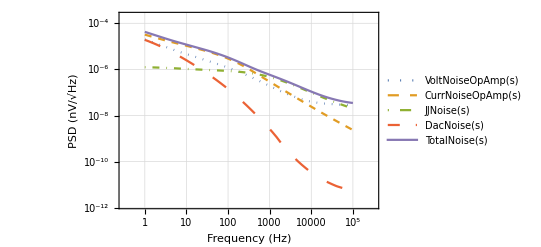

```mathematica
(* plot vs frequency for reference *)
LogLogPlot[{VoltNoiseOpAmp[s],CurrNoiseOpAmp[s],JJNoise[s],DacNoise[s],TotalNoise[s]},{s,1,100kk},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotStyle->{Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dashing[{.03,.04}]],Thick},FrameLabel->{Style["Frequency (Hz)",{Black,FontSize->15}], Style["PSD (nV/√Hz)",{Black,FontSize->15}]}]

(* styling for publication plot *)
(*publicationPlot=LogLogPlot[{VoltNoiseOpAmp[s],CurrNoiseOpAmp[s],JJNoise[s],DacNoise[s],TotalNoise[s]},{s,1,100kk},PlotRange->{{1,100kk},{10^-12,10^-4}},Frame->True,GridLines->Automatic,PlotStyle->{Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dashing[{.03,.04}]],Thick},FrameLabel->{MaTeX["\\text{Frequency} \\left(\\text{Hz}\\right)"],MaTeX["\\text{PSD}\,\,\\left(\\si[per-mode=symbol]{\\volt\\per\\sqrthz}\,\\right)"],Null,""},BaseStyle->texStyle];*)
(*Export[ParentDirectory[NotebookDirectory[]]<>"/fig/NoiseContrib.pdf",ImportString@ExportString[publicationPlot,"EPS"]]*)
```

```mathematica
exportTable=Table[{w,VoltNoiseOpAmp[w],CurrNoiseOpAmp[ w],JJNoise[w],DacNoise[w],TotalNoise[w]}/.w->10^s,{s,0,5,.05}];
Export["CalcNoiseContrib.csv",exportTable]
```

CalcNoiseContrib.csv

```mathematica
Print["Opamp voltage noise, 1Hz-100kHz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,1,10^5}]/uu, " uVrms"]
Print["Opamp current noise, 1Hz-100kHz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,1,10^5}]/uu," uVrms"]
Print["DAC voltage noise, 1Hz-100kHz: ",√NIntegrate[DacNoise[ s]^2,{s,1,10^5}]/uu, "uVrms"]
Print["Johnson noise, 1Hz-100kHz: ",√NIntegrate[JJNoise[s]^2,{s,1,10^5}]/uu, " uVrms"]
Print["Total noise, 1Hz-100kHz: ",√NIntegrate[TotalNoise[s]^2,{s,1,10^5}]/uu, " uVrms"];
```

Opamp voltage noise, 1Hz-100kHz: 37.506 uVrms

Opamp current noise, 1Hz-100kHz: 77.0434 uVrms

DAC voltage noise, 1Hz-100kHz: 22.5546uVrms

Johnson noise, 1Hz-100kHz: 31.1512 uVrms

Total noise, 1Hz-100kHz: 93.9228 uVrms

```mathematica
Print["Opamp voltage noise, 1Hz-10Hz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,1,10}]/uu, " uVrms"]
Print["Opamp current noise, 1Hz-10Hz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,1,10}]/uu," uVrms"]
Print["DAC voltage noise, 1Hz-10Hz: ",√NIntegrate[DacNoise[ s]^2,{s,1,10}]/uu, "uVrms"]
Print["Johnson noise, 1Hz-10Hz: ",√NIntegrate[JJNoise[s]^2,{s,1,10}]/uu, " uVrms"]
Print["Total noise, 1Hz-10Hz: ",√NIntegrate[TotalNoise[s]^2,{s,1,10}]/uu, " uVrms"];
```

Opamp voltage noise, 1Hz-10Hz: 25.7741 uVrms

Opamp current noise, 1Hz-10Hz: 49.1175 uVrms

DAC voltage noise, 1Hz-10Hz: 21.5038uVrms

Johnson noise, 1Hz-10Hz: 3.37207 uVrms

Total noise, 1Hz-10Hz: 59.5871 uVrms

```mathematica
Print["Opamp voltage noise, 10Hz-100kHz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,10,10^5}]/uu, " uVrms"]
Print["Opamp current noise, 10Hz-100kHz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,10,10^5}]/uu," uVrms"]
Print["DAC voltage noise, 10Hz-100kHz: ",√NIntegrate[DacNoise[ s]^2,{s,10,10^5}]/uu, "uVrms"]
Print["Johnson noise, 10Hz-100kHz: ",√NIntegrate[JJNoise[s]^2,{s,10,10^5}]/uu, " uVrms"]
Print["Total noise, 10Hz-100kHz: ",√NIntegrate[TotalNoise[s]^2,{s,10,10^5}]/uu, " uVrms"];
```

Opamp voltage noise, 10Hz-100kHz: 27.247 uVrms

Opamp current noise, 10Hz-100kHz: 59.3562 uVrms

DAC voltage noise, 10Hz-100kHz: 6.80429uVrms

Johnson noise, 10Hz-100kHz: 30.9681 uVrms

Total noise, 10Hz-100kHz: 72.6008 uVrms

```mathematica
√(60^2+73.^2)
```

94.4934

Finally, a few auxiliary calculations:

```mathematica
(* transfer function of low-pass filter on DAC *)
Zlp/(Rlp+Zlp)//FullSimplify//Factor
```

(1037.88 (142857.+1. s))/((4.95459+1. s) (3.0539×10^7+1. s))

This has a zero at roughly 23kHz:

```mathematica
142857.1428571429/(2Pi)
```

22736.4